Simple quartic 1D potential: double well:

```mathematica
a=1;b=1;
```

```mathematica
f[x_]=a x^4-b x^2+0.15x;
```

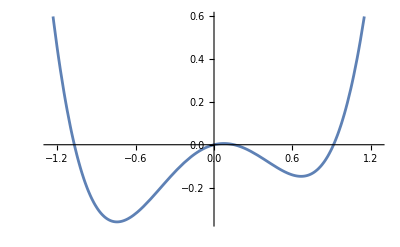

```mathematica
Plot[f[x],{x,-1.25,1.25}]
```

Simple 2D potential with the curved reaction path:

```mathematica
c=1;ky=0.5;kg=2.5;
```

```mathematica
g0[x_]=c x^2;
```

```mathematica
g1[x_]=8/(kg π)(Exp[-(π kg^2 x^2)/16]-1)+2x Erf[(kg √π)/4 x];
```

```mathematica
Plot[g1[x],{x,-10,10}]
```

```mathematica
u[x_,y_]=a x^4-b x^2+1/2 ky(y-g1[x])^2;
```

```mathematica
ucontour=ContourPlot[u[x,y],{x,-1,1},{y,-1,2},ContourShading->True,ColorFunction->Hue,Contours->50,PlotPoints->100];
```

```mathematica
Plot3D[u[x,y],{x,-1,1},{y,-1,3},ColorFunction->Hue,PlotPoints->100];
```

```mathematica
Plot[{u[q,-200]},{q,-0.2,0.2}];
```

```mathematica
Plot[{u[x,-0.5],u[x,0],u[x,0.5],u[x,1],u[x,1.5]},{x,-1.5,1.5}];
```

```mathematica
ux[x_,y_]=D[u[x,y],x];
```

```mathematica
uy[x_,y_]=D[u[x,y],y];
```

```mathematica
uxx[x_,y_]=D[u[x,y],{x,2}];
```

```mathematica
uyy[x_,y_]=D[u[x,y],{y,2}];
```

```mathematica
uxy[x_,y_]=D[u[x,y],x,y];
```

Reaction path:

```mathematica
p[x_]=Solve[uy[x,y]==0,y][[1]][[1]][[2]]
```

-1. (-1.01859 (-1.+ⅇ^(-1.22718 x^2))-2. x Erf[1.10778 x])

```mathematica
rpath=Plot[p[x],{x,-1,1}];
```

```mathematica
Show[GraphicsArray[{ucontour,rpath}]];
```

```mathematica
Show[ucontour,Graphics[{RGBColor[0,0,1],Thickness[0.01],Dashing[{0.02,0.02}],Line[Table[{0.1(i-11),p[0.1(i-11)]},{i,21}]]}]];
```

And now let's see the Hessian at athe saddle point (0,0) looks like:

```mathematica
{{uxx[0,0],uxy[0,0]},{uxy[0,0],uyy[0,0]}}//MatrixForm
```

(-2 | 0
0 | 0.1)